```mathematica
SetDirectory[NotebookDirectory[]];
pred=RGBColor[1,0,0,0.65];
pyellow=RGBColor[1,1,0,0.65];
pblue=RGBColor[173/255,216/255,230/255,0.65];
pgreen=RGBColor[1,0,1,0.65];
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#<-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#<0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#<Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#<Pi}}]&;
phase[l:{_?NumericQ..}]:=Module[{args=l},(args+Prepend[2Pi Accumulate@-IntegerPart@Differences[args/Pi],0])];
rasterizeBackground[g_,res_:100]:=Module[{raster},raster=Rasterize[Show[g,PlotRangePadding->0,ImagePadding->0,ImageMargins->0,PlotRangeClipping->False,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],If[Length[ImageSize/.Options[g]]==2,AspectRatio->(ImageSize/.Options[g])[[2]]/(ImageSize/.Options[g])[[1]],AspectRatio->(AspectRatio/.Options[g])]],ImageResolution->res];
Graphics[{Raster[raster[[1,1]],Transpose[PlotRange/.Quiet[AbsoluteOptions[g]]],raster[[1,3]]]},#]&@(Options[g]/.(Epilog->epi_):>Epilog->{})]
SetDirectory[NotebookDirectory[]]
```

/Users/zack/Documents/oscillators/uncorrelated

{2,500.,0.01}

{{runtime:,9.598926},{2,0.950000,1.000000,1,0.717968,2.016280}}

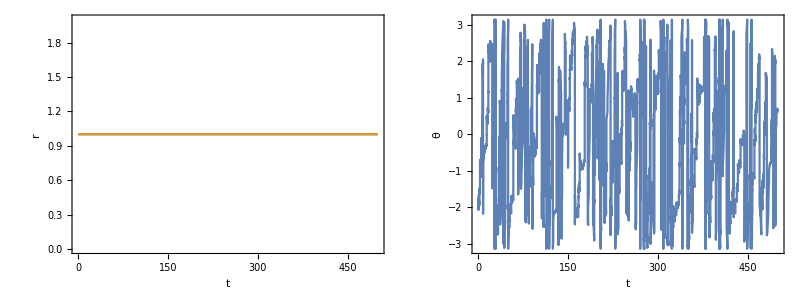

```mathematica
filebase="data/stest";
strlst=ReadList[filebase<>".out",String];
{n, t1, dt}=ToExpression[StringSplit[strlst[[1]]][[1;;3]]]
Nt=1+Floor[t1/dt];
StringSplit[strlst[[-2;;-1]]]
file=OpenRead[filebase<>".dat",BinaryFormat->True];
dat=Transpose[Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[file,"Real64"],2],2]];
Close[file];
Grid[{{ListPlot[Transpose[{Range[Nt]*dt,#}]&/@Abs[dat],Joined->True,Axes->False,Frame->True,FrameLabel->{t,r},LabelStyle->Directive[16],Joined->True,PlotRange->All,RotateLabel->False,ImageSize->350],ListPlot[Transpose[{Range[Nt]*dt,#}]&/@Arg[dat],Joined->True,Axes->False,Frame->True,FrameLabel->{t,θ},LabelStyle->Directive[16],Joined->True,PlotRange->All,RotateLabel->False,ImageSize->350]}}]
```

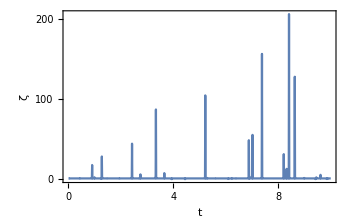

stuartnoise.pdf

```mathematica
file=OpenRead[filebase<>"noise.dat",BinaryFormat->True];
noise=Transpose[Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[file,"Real64"],2],2]];
Close[file];
p=ListPlot[Transpose[{Range[Nt]*dt,Abs[noise[[1]]]}][[1;;1000]],Joined->True,Axes->False,Frame->True,FrameLabel->{t,ζ},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->{{0,10},All},FrameTicks->{{Table[{i,i},{i,0,250,50}],Table[{i,""},{i,0,250,50}]},{Table[{i,i},{i,0,10,2}],Table[{i,""},{i,0,10,2}]}},ImageSize->350,ImagePadding->{{65,15},{65,15}}]
Export["stuartnoise.pdf",p]
```

General::munfl: 1.212697477×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.03268272903×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.9695504×10^-315 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

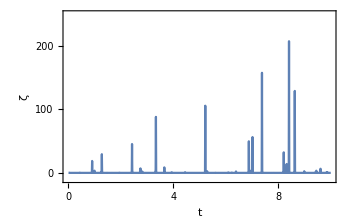

stuartnoise.pdf

```mathematica
file=OpenRead[filebase<>"noise2.dat",BinaryFormat->True];
noise=Transpose[Partition[BinaryReadList[file,"Real64"],2]];
Close[file];
p=ListPlot[Transpose[{Range[Nt]*dt,noise[[1]]}][[1;;1000]],Joined->True,Axes->False,Frame->True,FrameLabel->{t,ζ},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->{{0,10},{-10,250}},FrameTicks->{{Table[{i,i},{i,0,250,50}],Table[{i,""},{i,0,250,50}]},{Table[{i,i},{i,0,10,2}],Table[{i,""},{i,0,10,2}]}},ImageSize->350,ImagePadding->{{65,15},{65,15}}]
Export["stuartnoise.pdf",p]
```

ReadList::noopen: Cannot open data/snoise/correlatedaddconst0.out.

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦{3,5}⟧ is longer than depth of object.

ReadList::noopen: Cannot open data/snoise/correlatedaddconst1.out.

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ReadList::noopen: Cannot open data/snoise/correlatedaddconst2.out.

General::stop: Further output of ReadList::noopen will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

ReadList::noopen: Cannot open data/snoise/uncorrelatedaddconst0.out.

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦{3,5}⟧ is longer than depth of object.

ReadList::noopen: Cannot open data/snoise/uncorrelatedaddconst1.out.

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ReadList::noopen: Cannot open data/snoise/uncorrelatedaddconst2.out.

General::stop: Further output of ReadList::noopen will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

ReadList::noopen: Cannot open data/snoise/correlatedaddtrig0.out.

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦{3,5}⟧ is longer than depth of object.

ReadList::noopen: Cannot open data/snoise/correlatedaddtrig1.out.

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ReadList::noopen: Cannot open data/snoise/correlatedaddtrig2.out.

General::stop: Further output of ReadList::noopen will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

ReadList::noopen: Cannot open data/snoise/uncorrelatedaddtrig0.out.

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦{3,5}⟧ is longer than depth of object.

ReadList::noopen: Cannot open data/snoise/uncorrelatedaddtrig1.out.

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ReadList::noopen: Cannot open data/snoise/uncorrelatedaddtrig2.out.

General::stop: Further output of ReadList::noopen will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

ReadList::noopen: Cannot open data/snoise/correlatedmult0.out.

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦{3,5}⟧ is longer than depth of object.

ReadList::noopen: Cannot open data/snoise/correlatedmult1.out.

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ReadList::noopen: Cannot open data/snoise/correlatedmult2.out.

General::stop: Further output of ReadList::noopen will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

ReadList::noopen: Cannot open data/snoise/uncorrelatedmult0.out.

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦{3,5}⟧ is longer than depth of object.

ReadList::noopen: Cannot open data/snoise/uncorrelatedmult1.out.

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ReadList::noopen: Cannot open data/snoise/uncorrelatedmult2.out.

General::stop: Further output of ReadList::noopen will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦-1⟧].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringSplit[$Failed⟦-1⟧] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

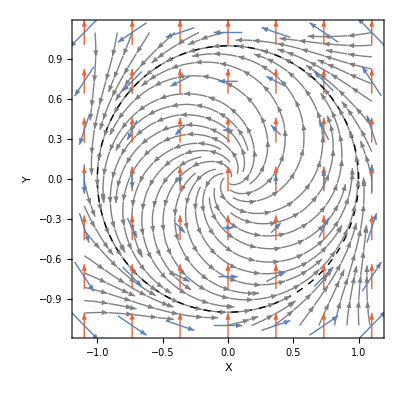
-Graphics- | -Graphics-

```mathematica
imgSize2={400,400};
imgPadding2={{95,5},{75,10}};
correlatedaddconst=Table[ToExpression[StringSplit[ReadList["data/snoise/correlatedadd1"<>ToString[i]<>".out",String][[-1]]]][[{3,5}]],{i,0,10}];
uncorrelatedaddconst=Table[ToExpression[StringSplit[ReadList["data/snoise/uncorrelatedadd1"<>ToString[i]<>".out",String][[-1]]]][[{3,5}]],{i,0,10}];
correlatedaddtrig=Table[ToExpression[StringSplit[ReadList["data/snoise/correlatedadd2"<>ToString[i]<>".out",String][[-1]]]][[{3,5}]],{i,0,10}];
uncorrelatedaddtrig=Table[ToExpression[StringSplit[ReadList["data/snoise/uncorrelatedadd2"<>ToString[i]<>".out",String][[-1]]]][[{3,5}]],{i,0,10}];
correlatedmult=Table[ToExpression[StringSplit[ReadList["data/snoise/correlatedmult"<>ToString[i]<>".out",String][[-1]]]][[{3,5}]],{i,0,10}];
uncorrelatedmult=Table[ToExpression[StringSplit[ReadList["data/snoise/uncorrelatedmult"<>ToString[i]<>".out",String][[-1]]]][[{3,5}]],{i,0,10}];
imgSize2={400,400};
imgPadding2={{95,5},{75,10}};
p5=ListPlot[{{#[[1]]-0.05,#[[2]]}&/@uncorrelatedaddconst,{#[[1]]-0.05,#[[2]]}&/@correlatedaddconst,uncorrelatedaddtrig,correlatedaddtrig,{#[[1]]+0.05,#[[2]]}&/@uncorrelatedmult,{#[[1]]+0.05,#[[2]]}&/@correlatedmult},Axes->False,Frame->True,FrameLabel->{δ,AngleBracket[R^2]},LabelStyle->Directive[24,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{-0.1,5.1},{0.45,1}},PlotMarkers->{{Graphics[{ColorData[97,"ColorList"][[1]],Disk[]}],0.05},{Graphics[{ColorData[97,"ColorList"][[1]],AbsoluteThickness[2],Circle[]}],0.05},{Graphics[{ColorData[97,"ColorList"][[4]],Rectangle[]}],0.05},{Graphics[{EdgeForm[Directive[ColorData[97,"ColorList"][[4]],AbsoluteThickness[2]]],FaceForm[None],Rectangle[]}],0.05},{Graphics[{Gray,Triangle[{{0,0},{1,0},{1/2,3^(1/2)/2}}]}],0.05},{Graphics[{EdgeForm[Directive[Gray,AbsoluteThickness[2]]],FaceForm[None],Triangle[{{0,0},{1,0},{1/2,3^(1/2)/2}}]}],0.05}},PlotStyle->{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[Gray],Directive[Gray]},AspectRatio->1,ImageSize->imgSize2,
ImagePadding->imgPadding2,Joined->True];
p1=StreamPlot[{x-y-(x^2+y^2)*x,y+x-(x^2+y^2)*y},{x,-1.1,1.1},{y,-1.1,1.1},LabelStyle->Directive[24,Black], FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{{Y,None},{X,None}},ImageSize->imgSize2,ImagePadding->imgPadding2,StreamStyle->Gray];
p2=VectorPlot[{-y,x},{x,-1.1,1.1},{y,-1.1,1.1},VectorPoints->Flatten[Table[{i,j},{i,-1.1,1.1,2.2/6},{j,-1.1,1.1,2.2/6}],1],VectorScale->0.1,VectorStyle->{Thick,ColorData[97,"ColorList"][[1]]}];
p3=VectorPlot[{0,1},{x,-1.1,1.1},{y,-1.1,1.1},VectorPoints->Flatten[Table[{i,j},{i,-1.1,1.1,2.2/6},{j,-1.1,1.1,2.2/6}],1],VectorScale->0.06,VectorStyle->{Thick,ColorData[97,"ColorList"][[4]]}];
p4=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->Directive[Black,Thick,Dashed]];
p0=Show[p1,p3,p2,p4,ImageSize->imgSize2,ImagePadding->imgPadding2];
p=Grid[{{p0,p5}}]
```

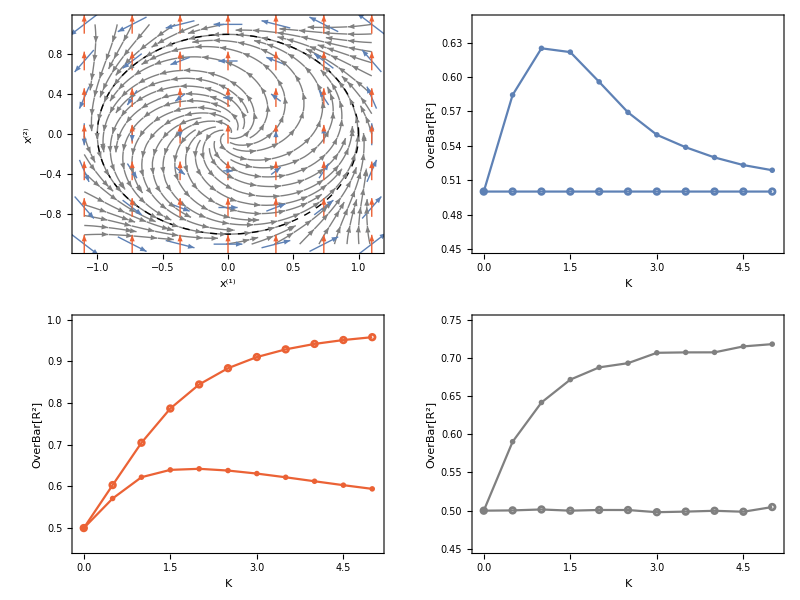

```mathematica
p1=StreamPlot[{x-y-(x^2+y^2)*x,y+x-(x^2+y^2)*y},{x,-1.1,1.1},{y,-1.1,1.1},LabelStyle->Directive[24,Black], FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{{Superscript[x,"(2)"],None},{Superscript[x,"(1)"],None}},ImageSize->imgSize2,ImagePadding->imgPadding2,StreamStyle->Gray];
p2=VectorPlot[{-y,x},{x,-1.1,1.1},{y,-1.1,1.1},VectorPoints->Flatten[Table[{i,j},{i,-1.1,1.1,2.2/6},{j,-1.1,1.1,2.2/6}],1],VectorScale->0.1,VectorStyle->{Thick,ColorData[97,"ColorList"][[1]]}];
p3=VectorPlot[{0,1},{x,-1.1,1.1},{y,-1.1,1.1},VectorPoints->Flatten[Table[{i,j},{i,-1.1,1.1,2.2/6},{j,-1.1,1.1,2.2/6}],1],VectorScale->0.06,VectorStyle->{Thick,ColorData[97,"ColorList"][[4]]}];
p4=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->Directive[Black,Thick,Dashed]];
p0=Show[p1,p2,p3,p4,ImageSize->imgSize2,ImagePadding->imgPadding2];

p=Grid[{{p0,ListPlot[{uncorrelatedaddconst,correlatedaddconst},Axes->False,Frame->True,FrameLabel->{K,OverBar[R^2]},LabelStyle->Directive[24,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{-0.1,5.1},{0.45,0.65}},PlotMarkers->{{Graphics[{ColorData[97,"ColorList"][[1]],Disk[]}],0.05},{Graphics[{ColorData[97,"ColorList"][[1]],AbsoluteThickness[2],Circle[]}],0.05}},PlotStyle->Directive[ColorData[97,"ColorList"][[1]]],AspectRatio->1,ImageSize->imgSize2,
ImagePadding->imgPadding2,Joined->True]},{ListPlot[{uncorrelatedaddtrig,correlatedaddtrig},Axes->False,Frame->True,FrameLabel->{K,OverBar[R^2]},LabelStyle->Directive[24,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{-0.1,5.1},{0.45,1}},PlotMarkers->{{Graphics[{ColorData[97,"ColorList"][[4]],Disk[]}],0.05},{Graphics[{ColorData[97,"ColorList"][[4]],AbsoluteThickness[2],Circle[]}],0.05}},PlotStyle->Directive[ColorData[97,"ColorList"][[4]]],AspectRatio->1,ImageSize->imgSize2,
ImagePadding->imgPadding2,Joined->True],ListPlot[{uncorrelatedmult,correlatedmult},Axes->False,Frame->True,FrameLabel->{K,OverBar[R^2]},LabelStyle->Directive[24,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{-0.1,5.1},{0.45,0.75}},PlotMarkers->{{Graphics[{Gray,Disk[]}],0.05},{Graphics[{Gray,AbsoluteThickness[2],Circle[]}],0.05}},PlotStyle->Directive[Gray],AspectRatio->1,ImageSize->imgSize2,
ImagePadding->imgPadding2,Joined->True]}}]
```

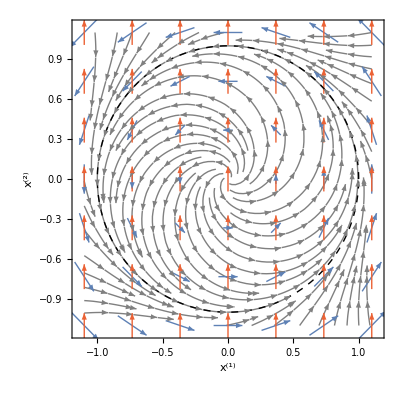
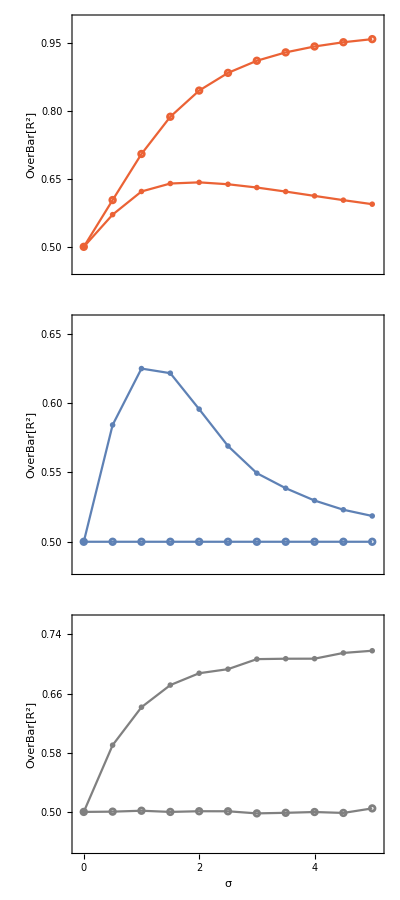
-Graphics- | -Graphics-

plots/fig4.pdf

```mathematica
p=Grid[{{p0,Grid[{{ListPlot[{uncorrelatedaddtrig,correlatedaddtrig},Axes->False,Frame->True,FrameLabel->{None,OverBar[R^2]},LabelStyle->Directive[24,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{-0.1,5.1},{0.45,1.0}},PlotMarkers->{{Graphics[{ColorData[97,"ColorList"][[4]],Disk[]}],0.15},{Graphics[{ColorData[97,"ColorList"][[4]],AbsoluteThickness[2],Circle[]}],0.15}},FrameTicks->{{Table[{r,PaddedForm[r,{3,2}]},{r,0.5,0.96,0.15}],Table[{r,""},{r,0.5,0.96,0.15}]},{Table[{i,""},{i,0,5}],Table[{i,""},{i,0,5}]}},ImagePadding->{{100,10},{10,10}},PlotStyle->Directive[ColorData[97,"ColorList"][[4]]],AspectRatio->1/3,ImageSize->375,Joined->True]},{ListPlot[{uncorrelatedaddconst,correlatedaddconst},Axes->False,Frame->True,FrameLabel->{None,OverBar[R^2]},LabelStyle->Directive[24,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{-0.1,5.1},{0.48,0.66}},PlotMarkers->{{Graphics[{ColorData[97,"ColorList"][[1]],Disk[]}],0.15},{Graphics[{ColorData[97,"ColorList"][[1]],AbsoluteThickness[2],Circle[]}],0.15}},FrameTicks->{{Table[{r,PaddedForm[r,{3,2}]},{r,0.5,0.65,0.05}],Table[{r,""},{r,0.5,0.65,0.05}]},{Table[{i,""},{i,0,5}],Table[{i,""},{i,0,5}]}},ImagePadding->{{100,10},{10,10}},PlotStyle->Directive[ColorData[97,"ColorList"][[1]]],AspectRatio->1/3,ImageSize->375,Joined->True]},{ListPlot[{uncorrelatedmult,correlatedmult},Axes->False,Frame->True,FrameLabel->{σ,OverBar[R^2]},LabelStyle->Directive[24,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{-0.1,5.1},{0.45,0.76}},PlotMarkers->{{Graphics[{Gray,Disk[]}],0.15},{Graphics[{Gray,AbsoluteThickness[2],Circle[]}],0.15}},FrameTicks->{{Table[{r,PaddedForm[r,{3,2}]},{r,0.5,0.8,0.08}],Table[{r,""},{r,0.5,0.8,0.08}]},{Table[{i,i},{i,0,5}],Table[{i,""},{i,0,5}]}},ImagePadding->{{100,10},{100,10}},PlotStyle->Directive[Gray],AspectRatio->1/3,ImageSize->375,Joined->True]}}]}}]
Export["plots/fig4.pdf",p]
```

```mathematica
Z={D[ArcTan[y,x],x],D[ArcTan[y,x],y]}
h=Simplify[{Re[#],Im[#]}&@Expand[1/2*((x+I*y)*(u-I*v)-(u+I*v)*(x-I*y))*(x+I*y)],Element[x,Reals]&&Element[y,Reals]&&Element[u,Reals]&&Element[v,Reals]]
g1={y,-x}
g2={0,1}
```

{y/(x^2+y^2),-x/(x^2+y^2)}

{y (v x-u y),x (-v x+u y)}

{y,-x}

{0,1}

```mathematica
Integrate[Z.h/(2*Pi)/.{x->Cos[θ1+ϕ],y->Sin[θ1+ϕ],u->Cos[θ2+ϕ],v->Sin[θ2+ϕ]},{ϕ,0,Pi}]
FullSimplify[Z.g1/.{x->Cos[θ1],y->Sin[θ1]}]
FullSimplify[Z.g2/.{x->Cos[θ1],y->Sin[θ1]}]
```

-1/2 Sin[θ1-θ2]

1

-Cos[θ1]

```mathematica
z[n_,t_]:=r[n,t]*Exp[I*θ[n,t]]
zc[n_,t_]:=r[n,t]*Exp[-I*θ[n,t]]
Simplify[zc[1,t]*ζ[1,t]*((1+I*α[1])*z[1,t]-z[1,t]*zc[1,t]*z[1,t]-K/2*(z[1,t]*Z[2,t]-z[2,t]*zc[1,t])*z[1,t])+z[1,t]*ζ[1,t]*((1-I*α[1])*zc[1,t]-z[1,t]*zc[1,t]*zc[1,t]-K/2*(zc[1,t]*z[2,t]-Z[2,t]*z[1,t])*zc[1,t])]
FullSimplify[1/(2*I)*(1/z[1,t]*ζ[1,t]*((1+I*α[1])*z[1,t]-z[1,t]*zc[1,t]*z[1,t]+K/2*(z[1,t]*zc[2,t]-z[2,t]*zc[1,t])*z[1,t])-1/zc[1,t]*ζ[1,t]*((1-I*α[1])*zc[1,t]-z[1,t]*zc[1,t]*zc[1,t]+K/2*(zc[1,t]*z[2,t]-zc[2,t]*z[1,t])*zc[1,t]))]
```

-2 r[1,t]^2 (-1+r[1,t]^2) ζ[1,t]

(K r[1,t] r[2,t] Sin[θ[1,t]-θ[2,t]]+α[1]) ζ[1,t]